```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-6,2},{m,-6,2}]]],{x,-6,2},{y,-6,2},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
ρ:=0.3
```

```mathematica
points:={{0.4,0.1},{0.22924952910108745,0.19350621025416642},{0.05283194463606211,0.7046886632281584},{0.06177169928112605,0.2935715537444358},{0.768731955664866,1.8089107756324223},{-1.7549257396828621,1.1730277634658894},{-1.278253524817416,1.887861799877635},{-1.700617935559081,1.9807547540651356},{-1.299563417407707,2.0161789663148117},{-1.7168158123204487,2.0990288637129226},{-1.1661377215190767,2.7502035679028825}}
```

```mathematica
(* println(collisions([0.5,0.1],[-0.42,0.23],0.3,10)[1]) *)
```

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
{{0.0,0.35},{0.9641445552106563,0.9066491184885844},{1.901566855409655,-1.982367188367812},{1.0999748803884173,-2.9977587299757396},{1.9177056142378983,-3.9431877295644826},{-5.930360381365476,-1.07176575448247},{-4.990843003801113,-3.900420135465981},{-3.997705464350009,-2.099973672064954}}
```

```mathematica
ρ:=0.1
```

```mathematica
points:={{0.0,0.35},{0.9641445552106563,0.9066491184885844},{1.901566855409655,-1.982367188367812},{1.0999748803884173,-2.9977587299757396},{1.9177056142378983,-3.9431877295644826},{-5.930360381365476,-1.07176575448247},{-4.990843003801113,-3.900420135465981},{-3.997705464350009,-2.099973672064954}}
```

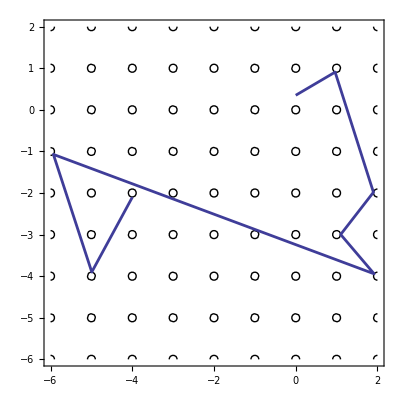

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```